```mathematica
<<"Dynamica_1011.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
projectHomeDir="./";
lineThickness=0.012;
legendThickness=lineThickness*20;
labelSize=22;
tickSize=17;
legendSize=19;
textSize=22;
(*colours=ColorData[97,"ColorList"];*)
(*Coulour-blind frendly colour set *)
colours={RGBColor["#56B4E9"],RGBColor["#009E73"],RGBColor["#F0E442"],RGBColor["#0072B2"],RGBColor["#D55E00"],RGBColor["#CC79A7"],RGBColor["#999999"],RGBColor["#E69F00"]};
(*colours={RGBColor["#e41a1c"],RGBColor["#377eb8"],RGBColor["#4daf4a"],RGBColor["#984ea3"],RGBColor["#ff7f00"],RGBColor["#ffff33"]};*)
colours={RGBColor["#000000"],RGBColor["#3DB7E9"],RGBColor["#F748A5"],RGBColor["#359B73"],RGBColor["#e69f00"],RGBColor["#2271B2"],RGBColor["#f0e442"],RGBColor["#d55e00"]}
```

{RGBColor[0., 0., 0.],RGBColor[0.23921568627450981, 0.7176470588235294, 0.9137254901960784],RGBColor[0.9686274509803922, 0.2823529411764706, 0.6470588235294118],RGBColor[0.20784313725490197, 0.6078431372549019, 0.45098039215686275],RGBColor[0.9019607843137255, 0.6235294117647059, 0.],RGBColor[0.13333333333333333, 0.44313725490196076, 0.6980392156862745],RGBColor[0.9411764705882353, 0.8941176470588236, 0.25882352941176473],RGBColor[0.8352941176470589, 0.3686274509803922, 0.]}

### Analysis of the systems with normal Mathematica functions (Solve ...)

#### Define the system for Direct Switch with noise as a normal Mathematica system

```mathematica
Clear[q,qA,qB,w,A]
systemDSnoise={
(qA-qB) A(1-A)+w(1-2A)}
(*(q-1) A(1-A)+w(1-2A)}*)
simple=True;
fixedPointsDSnoise=If[simple,Simplify[Solve[{systemDSnoise==0},{A}]],Solve[{systemDSnoise==0},{A}]]
"Found "<>ToString[Length[fixedPointsDSnoise]]<>" fixed points"
```

{(1-A) A (qA-qB)+(1-2 A) w}

{{A→(qA-qB-2 w+√(qA^2-2 qA qB+qB^2+4 w^2))/(2 qA-2 qB)},{A→(-qA+qB+2 w+√(qA^2-2 qA qB+qB^2+4 w^2))/(2 (-qA+qB))}}

Found 2 fixed points

Stability of fixed point 1:
                             2               2      2
      qA - qB - 2 w + Sqrt[qA  - 2 qA qB + qB  + 4 w ]
{A -> ------------------------------------------------}
                        2 qA - 2 qB

Instable eigen1

False

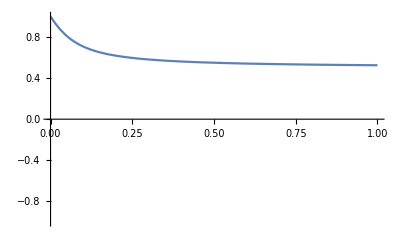

Stability of fixed point 2:
                              2               2      2
      -qA + qB + 2 w + Sqrt[qA  - 2 qA qB + qB  + 4 w ]
{A -> -------------------------------------------------}
                        2 (-qA + qB)

Instable eigen1

qB>0&&((0<qA<qB&&w≥0)||(qA==qB&&w>0)||(qA>qB&&w≥0))

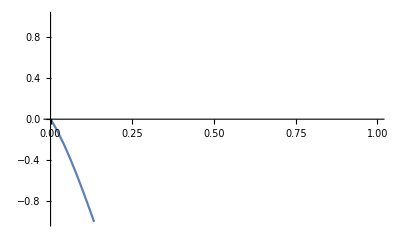

```mathematica
der2=Simplify[D[systemDSnoise,A]];
Do[
Print[Style["Stability of fixed point "<>ToString[solN]<>":\n"<>ToString[fixedPointsDSnoise[[solN]]],Bold,FontSize->15,Blue]];
der2WithSol=der2/.fixedPointsDSnoise[[solN]];
"Eigenvalues";
eigen=Eigenvalues[der2WithSol];
Print[Style["Instable eigen1",Italic]];
Print[Reduce[eigen[[1]]>0&&0≤w&&qA>0&&qB>0,w,Reals]];
Print[Plot[{fixedPointsDSnoise⟦solN⟧⟦1,2⟧/.{q->1.2,qA->1,qB->0.8}},{w,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
(*Print[Reduce[eigen[[1]]>0&&0≤w&&qA>0&&qB>0,w,Reals]];
Print[Plot[{fixedPointsDSnoise⟦solN⟧⟦1,2⟧/.{qA->1,qB->0.8}},{w,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];*)
,{solN,Range[1,Length[fixedPointsDSnoise]]}]
```

#### The stable point is fixed point n. 1:

```mathematica
stablePoint=1;
FullSimplify[fixedPointsDSnoise[[stablePoint,1,2]]]
Collect[fixedPointsDSnoise[[stablePoint,1,2]],qA-qB]
Print[TeXForm[%/.{qA->Subscript[q, x],qB->Subscript[q, y],w->σ}]]
FullSimplify[1-2 q+q^2+4 w^2]
Print[TeXForm[%/.{w->σ}]]
```

(qA-qB-2 w+√((qA-qB)^2+4 w^2))/(2 (qA-qB))

(qA-qB)/(2 qA-2 qB)+(-2 w+√(qA^2-2 qA qB+qB^2+4 w^2))/(2 qA-2 qB)

\frac{\sqrt{-2 q_x q_y+q_x^2+q_y^2+4 \sigma ^2}-2 \sigma }{2 q_x-2 q_y}+\frac{q_x-q_y}{2 q_x-2 q_y}

(-1+q)^2+4 w^2

(q-1)^2+4 \sigma ^2

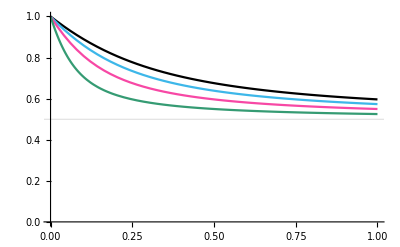

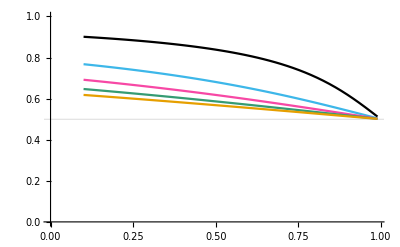

```mathematica
lines=Table[fixedPointsDSnoise[[stablePoint,1,2]]/.{qA->1},{qB,Range[0.2,0.8,0.2]}];
Plot[lines,{w,0,1},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->colours]
lines=Table[fixedPointsDSnoise[[stablePoint,1,2]]/.{qA->1},{w,Range[0.1,1,0.2]}];
Plot[lines,{qB,0.1,0.99},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->colours]
```

#### Voter model with quality ratio q and zealot size (with z/2 in each equal size A and B)

```mathematica
Clear[A,z,q]
systemDSzealots={
(q-1)A (1-A-2z)+z(q(1-A-2z)-A )}
simple=True;
fixedPointsDSzealots=If[simple,Simplify[Solve[{systemDSzealots==0},{A}]],Solve[{systemDSzealots==0},{A}]]
"Found "<>ToString[Length[fixedPointsDSzealots]]<>" fixed points"
```

{A (-1+q) (1-A-2 z)+(-A+q (1-A-2 z)) z}

{{A→(-1+q+z-3 q z+√((-1+z)^2+q^2 (-1+z)^2+2 q (-1+2 z+z^2)))/(2 (-1+q))},{A→(-1+q+z-3 q z-√((-1+z)^2+q^2 (-1+z)^2+2 q (-1+2 z+z^2)))/(2 (-1+q))}}

Found 2 fixed points

Stability of fixed point 1:
                                        2    2         2                    2
      -1 + q + z - 3 q z + Sqrt[(-1 + z)  + q  (-1 + z)  + 2 q (-1 + 2 z + z )]
{A -> -------------------------------------------------------------------------}
                                     2 (-1 + q)

Instable eigen1

False

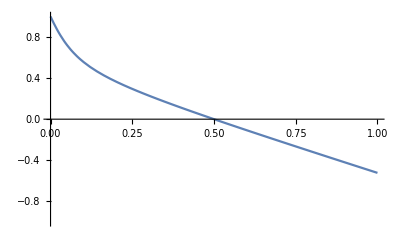

Stability of fixed point 2:
                                        2    2         2                    2
      -1 + q + z - 3 q z - Sqrt[(-1 + z)  + q  (-1 + z)  + 2 q (-1 + 2 z + z )]
{A -> -------------------------------------------------------------------------}
                                     2 (-1 + q)

Instable eigen1

(0<q<1&&z≥0)||(q==1&&z>0)||(q>1&&z≥0)

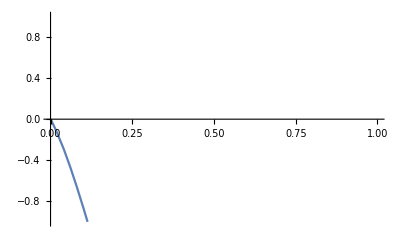

```mathematica
der2=Simplify[D[systemDSzealots,A]];
Do[
Print[Style["Stability of fixed point "<>ToString[solN]<>":\n"<>ToString[fixedPointsDSzealots[[solN]]],Bold,FontSize->15,Blue]];
der2WithSol=der2/.fixedPointsDSzealots[[solN]];
"Eigenvalues";
eigen=Eigenvalues[der2WithSol];
Print[Style["Instable eigen1",Italic]];
Print[Reduce[eigen[[1]]>0&&0≤z&&q>0,z,Reals]];
Print[Plot[{fixedPointsDSzealots⟦solN⟧⟦1,2⟧/.{q->1.2}},{z,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
,{solN,Range[1,Length[fixedPointsDSzealots]]}]
```

#### The stable point is fixed point n. 1:

```mathematica
FullSimplify[fixedPointsDSzealots[[1,1,2]]]
Print[TeXForm[%]]
Collect[fixedPointsDSzealots[[1,1,2]],q-1]
Print[TeXForm[%]]
```

(-1+q+z-3 q z+√((-1+q)^2-2 (-1+q)^2 z+(1+q)^2 z^2))/(2 (-1+q))

\frac{\sqrt{(q+1)^2 z^2-2 (q-1)^2 z+(q-1)^2}-3 q z+q+z-1}{2 (q-1)}

1/2+(z-3 q z+√((-1+z)^2+q^2 (-1+z)^2+2 q (-1+2 z+z^2)))/(2 (-1+q))

\frac{\sqrt{q^2 (z-1)^2+2 q \left(z^2+2 z-1\right)+(z-1)^2}-3 q z+z}{2 (q-1)}+\frac{1}{2}

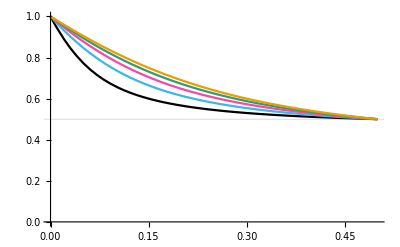

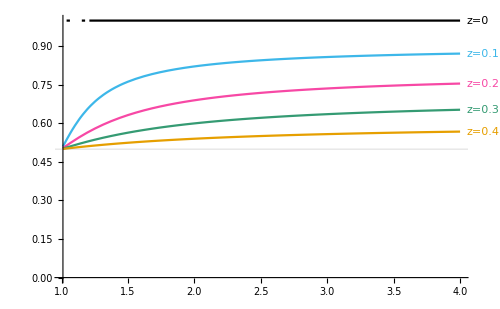

```mathematica
(*colours=ColorData["Indexed","ColorList"][[97]];*)
lines=Table[fixedPointsDSzealots[[1,1,2]]+z,{q,Range[1.2,2,0.2]}];
Plot[lines,{z,0,0.5},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->colours]

zRange=Join[{0},Range[0.1,0.4,0.1]];
(*zText=Range[1.03,1.03-0.081*Length[zRange],-0.06];*)
zText=Table[fixedPointsDSzealots[[1,1,2]]+z/.{z->i,q->4},{i,zRange}];
lines=Table[fixedPointsDSzealots[[1,1,2]]+z,{z,zRange}];
Show[
Plot[lines,{q,1.01,4},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->colours],
Table[
Graphics[
Style[Text["z="<>ToString[zRange[[zi]]],{4.05,zText[[zi]]},{-1,0}],
Directive[{colours[[zi]],14,Bold}],TextAlignment->Right
]
],
{zi,Range[1,Length[zRange]]} ],
ImageSize->500,
ImagePadding->{{70,105},{50,20}},PlotRangeClipping->False]
```

#### Define the system for Cross-Inhibition with zealots as a normal Mathematica system

```mathematica
Clear[q,z,A,B]
systemCIzealots={
q(A+z)(1-A-B-2z)-A(B+z),
(B+z)(1-A-B-2z)-q B(A+z)
}
simple=False;
fixedPointsCIzealots=If[simple,Simplify[Solve[{systemCIzealots==0},{A,B}]],Solve[{systemCIzealots==0},{A,B}]]
"Found "<>ToString[Length[fixedPointsCIzealots]]<>" fixed points"
```

{q (1-A-B-2 z) (A+z)-A (B+z),-B q (A+z)+(1-A-B-2 z) (B+z)}

{{A→-z,B→-z},{A→-(7+1)/(3 (1))-1+1,B→1},{1},{A→-(-2-q-q^2+3 z+4 q z+4 q^2 z)/(3 (1+q+q^2))+((1-ⅈ √3) (-(-2-q-q^2+1+4 q z+4 q^2 z)^2+3 (1+q+q^2) (8+3 q z^2+5 q^2 z^2)))/(3 2^(2/3) (1+q+q^2) (42+√(1^2+4 1))^(1/3))-((1+ⅈ √3) (-2-3 q+39+√((1)^2+4 1^3))^(1/3))/(6 2^(1/3) (1+q+q^2)),B→(-z-q z+50)/(-z-q z+z^2)}}
 |  |  |  |

Found 4 fixed points

Plot of fixed point 1

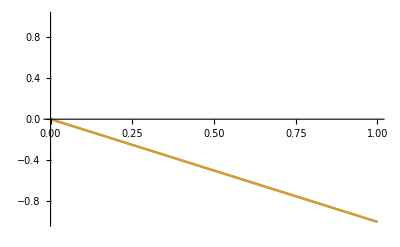

Plot of fixed point 2

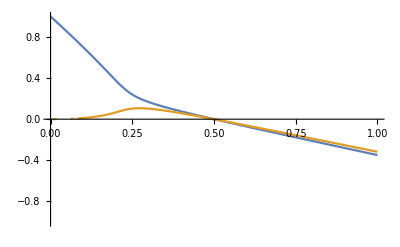

Plot of fixed point 3

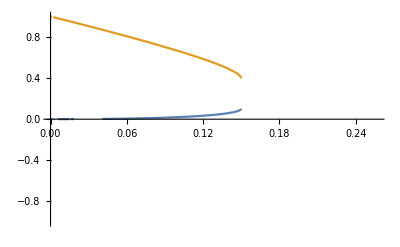

Plot of fixed point 4

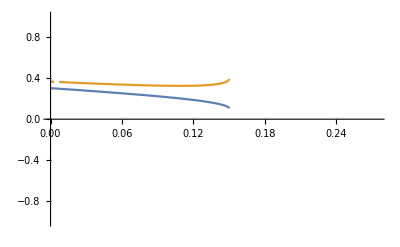

```mathematica
params={q->1.1};
Do[
Print[Style["Plot of fixed point "<>ToString[solN],Bold,FontSize->15,Blue]];
plt=Plot[{fixedPointsCIzealots⟦solN⟧⟦1,2⟧/.params,fixedPointsCIzealots⟦solN⟧⟦2,2⟧/.params},{z,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}];
Print[plt]
,{solN,Range[1,Length[fixedPointsCIzealots]]}]
```

Plot Figure 4(E) for Cross-inhibition

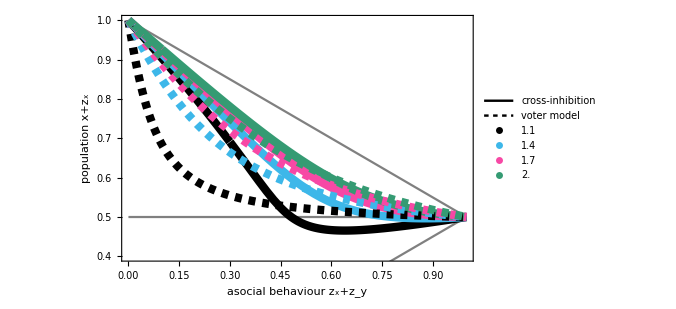

```mathematica
(*colours=ColorData["Indexed","ColorList"][[97]];*)
saveImg=False;
qRange=Range[1.1,2,0.3];
linesCI=Table[fixedPointsCIzealots[[2,1,2]]+z,{q,qRange}]/.{z->z/2};
linesDS=Table[fixedPointsDSzealots[[1,1,2]]+z,{q,qRange}]/.{z->z/2};
plt=Show[
(*Table[
Plot[lines[[qi]],{z,0,0.5},PlotStyle->Directive[{colours[[qi]],Thickness[lineThickness]}]
],
{qi,Range[1,Length[qRange]]} ],*)
Plot[{1-z/2,z/2,0.5},{z,0,1},PlotStyle->Directive[{Gray}],
PlotLegends->Placed[
LineLegend[Table[Directive[{Dashing[i],Thickness[lineThickness]}],{i,{1,0.013}}],{"cross-inhibition","voter model"},LegendLayout->"Column",LegendMarkerSize->{50,10},
LabelStyle->tickSize,LegendFunction->Panel
],{0.77,0.61}]
],
Plot[linesCI,{z,0,1},PlotStyle->Table[Directive[{colours[[i]],Thickness[lineThickness]}],{i,6}]],
Plot[linesDS,{z,0,1},PlotStyle->Table[Directive[{colours[[i]],Thickness[lineThickness],Dashed}],{i,6}],
PlotLegends->Placed[
PointLegend[colours,qRange,LegendLayout->"Row",LegendMarkerSize->30,LegendFunction->Panel,
LegendLabel->Style["quality ratio q",legendSize],LabelStyle->tickSize
],{0.645,0.85}]],
PlotRange->{{0,1},{0.4,1}},Axes->False,FrameStyle->Directive[{Thickness[.005]}],
ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"asocial behaviour z_x+z_y","population x+z_x"}
]
If[saveImg,Export[projectHomeDir<>"/graphics/fig4_panels/ODE-compare.pdf",plt]];
```

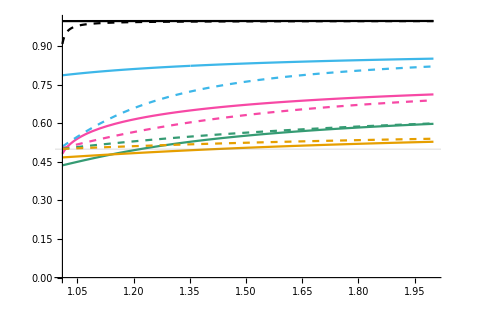

```mathematica
maxQ=2;
zRange=Join[{0.001},Range[0.1,0.4,0.1]];
(*zText=Range[1.03,1.03-0.081*Length[zRange],-0.06];*)
zText=Table[fixedPointsCIzealots[[2,1,2]]+z/.{z->i,q->maxQ},{i,zRange}];
lines=Table[fixedPointsCIzealots[[2,1,2]]+z,{z,zRange}];
linesDS=Table[fixedPointsDSzealots[[1,1,2]]+z,{z,zRange}];
Show[
Plot[lines,{q,1.01,maxQ},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->colours],
Plot[linesDS,{q,1.01,maxQ},
PlotRange->{0,1},GridLines->{{},{0.5}},PlotStyle->Table[Directive[{colours[[i]],Dashed}],{i,6}]],
Table[
Graphics[
Style[Text["z="<>ToString[zRange[[zi]]],{maxQ+.05,zText[[zi]]},{-1,0}],
Directive[{colours[[zi]],14,Bold}],TextAlignment->Right
]
],
{zi,Range[1,Length[zRange]]} ],
ImageSize->500,
ImagePadding->{{70,105},{50,20}},PlotRangeClipping->False]
```

#### Computing the analytical form of the bifurcation point for the Cross-inhibition Model (q != 1) and zealots

```mathematica
fixedPointsCIzealots[[3]][[1,2]]
```

-(-2-q-q^2+3 z+4 q z+4 q^2 z)/(3 (1+q+q^2))+((1+ⅈ √3) (-(-2-q-q^2+3 z+4 q z+4 q^2 z)^2+3 (1+q+q^2) (1-2 z-q z-2 q^2 z+z^2+3 q z^2+5 q^2 z^2)))/(3 2^(2/3) (1+q+q^2) (-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3+√((-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3)^2+4 (-(-2-q-q^2+3 z+4 q z+4 q^2 z)^2+3 (1+q+q^2) (1-2 z-q z-2 q^2 z+z^2+3 q z^2+5 q^2 z^2))^3))^(1/3))-1/(6 2^(1/3) (1+q+q^2))(1-ⅈ √3) (-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3+√((-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3)^2+4 (-(-2-q-q^2+3 z+4 q z+4 q^2 z)^2+3 (1+q+q^2) (1-2 z-q z-2 q^2 z+z^2+3 q z^2+5 q^2 z^2))^3))^(1/3)

```mathematica
sol3disap=
Solve[((-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3)^2+4 (-(-2-q-q^2+3 z+4 q z+4 q^2 z)^2+3 (1+q+q^2) (1-2 z-q z-2 q^2 z+z^2+3 q z^2+5 q^2 z^2))^3)==0,z];
sol3disapOnQ=
Solve[((-2-3 q+8 q^3+9 q^4+6 q^5+2 q^6-9 z-33 q z-48 q^2 z-54 q^3 z-42 q^4 z-27 q^5 z-6 q^6 z+36 z^2+108 q z^2+183 q^2 z^2+192 q^3 z^2+120 q^4 z^2+45 q^5 z^2+6 q^6 z^2-27 z^3-72 q z^3-135 q^2 z^3-128 q^3 z^3-87 q^4 z^3-24 q^5 z^3-2 q^6 z^3)^2+4 (-(-2-q-q^2+3 z+4 q z+4 q^2 z)^2+3 (1+q+q^2) (1-2 z-q z-2 q^2 z+z^2+3 q z^2+5 q^2 z^2))^3)==0,q];
```

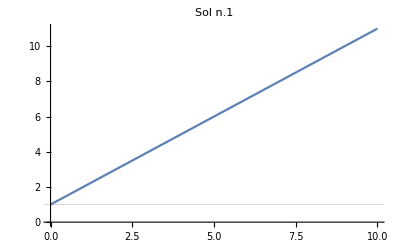

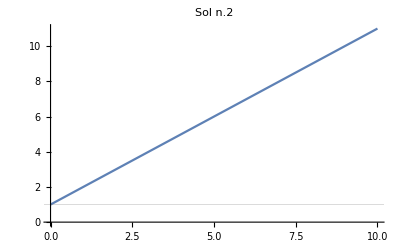

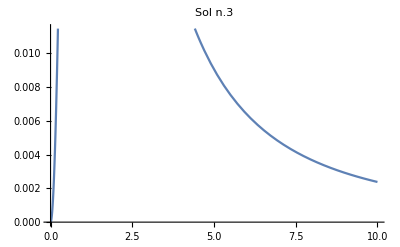

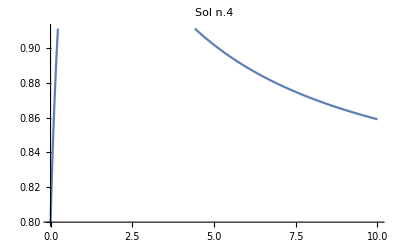

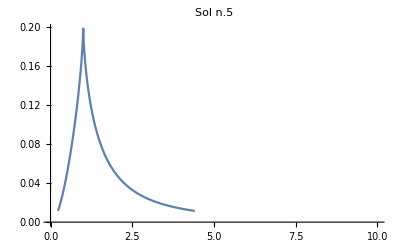

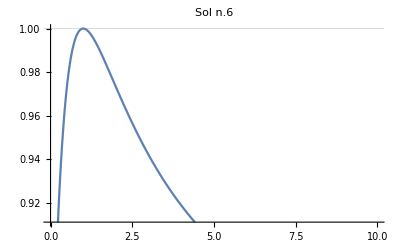

```mathematica
Do[
Print[Plot[sol3disap⟦solN⟧⟦1,2⟧/.{r->1.2},{q,0,10},GridLines->{{},{1}},PlotLabel->"Sol n."<>ToString[solN]]],
{solN,Range[1,Length[sol3disap]]}
]
```

```mathematica
bifPointCIzealotAsym=sol3disap[[5,1,2]];
bifPointCIzealotAsymFuncLowQ=sol3disapOnQ[[9,1,2]];
bifPointCIzealotAsymFuncHighQ=sol3disapOnQ[[10,1,2]]
```

-(-1+9 z-25 z^2+19 z^3)/(2 (-1+z)^2 (-4+5 z))+1/2 √(((-1+9 z-25 z^2+19 z^3)^2)/((-1+z)^4 (-4+5 z)^2)+(-8 z+26 z^2-28 z^3+10 z^4)/(-4 z+13 z^2-14 z^3+5 z^4)-(1-4 z+28 z^2-72 z^3+39 z^4)/((-1+z)^2 z (-4+5 z)))+1/2 √((2 (-1+9 z-25 z^2+19 z^3)^2)/((-1+z)^4 (-4+5 z)^2)-(-8 z+26 z^2-28 z^3+10 z^4)/(-4 z+13 z^2-14 z^3+5 z^4)-(1-4 z+28 z^2-72 z^3+39 z^4)/((-1+z)^2 z (-4+5 z))+(-(16 (-1+9 z-25 z^2+19 z^3))/((-1+z)^2 (-4+5 z))-(8 (-1+9 z-25 z^2+19 z^3)^3)/((-1+z)^6 (-4+5 z)^3)+(8 (-1+9 z-25 z^2+19 z^3) (1-4 z+28 z^2-72 z^3+39 z^4))/((-1+z)^4 z (-4+5 z)^2))/(4 √(((-1+9 z-25 z^2+19 z^3)^2)/((-1+z)^4 (-4+5 z)^2)+(-8 z+26 z^2-28 z^3+10 z^4)/(-4 z+13 z^2-14 z^3+5 z^4)-(1-4 z+28 z^2-72 z^3+39 z^4)/((-1+z)^2 z (-4+5 z)))))

#### Define the system for the symmetric (q=1) Cross-Inhibition model with zealot as a normal Mathematica system

```mathematica
Clear[q,z,A,B]
systemCIzealotsSym={
(A+z)(1-A-B-2z)-A(B+z),
(B+z)(1-A-B-2z)-B(A+z)
}
simple=True;
fixedPointsCIzealotsSym=If[simple,Simplify[Solve[{systemCIzealotsSym==0},{A,B}]],Solve[{systemCIzealotsSym==0},{A,B}]]
"Found "<>ToString[Length[fixedPointsCIzealotsSym]]<>" fixed points"
```

{(1-A-B-2 z) (A+z)-A (B+z),-B (A+z)+(1-A-B-2 z) (B+z)}

{{A→1/3 (1-2 z),B→1/3 (1-2 z)},{A→-z,B→-z},{A→1/2 (1-3 z-√(1-6 z+5 z^2)),B→1/2 (1-3 z+√(1-6 z+5 z^2))},{A→1/2 (1-3 z+√(1-6 z+5 z^2)),B→1/2 (1-3 z-√(1-6 z+5 z^2))}}

Found 4 fixed points

Stability of fixed point 1

Instable eigen1

0≤z<1/5

Instable eigen2

False

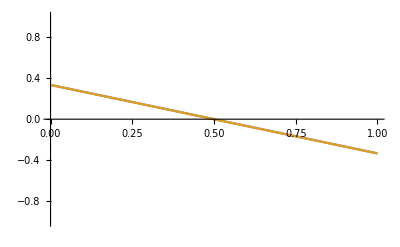

Stability of fixed point 2

Instable eigen1

0≤z<1

Instable eigen2

0≤z≤1

-Graphics-

Stability of fixed point 3

Instable eigen1

False

Instable eigen2

1/5<z≤1

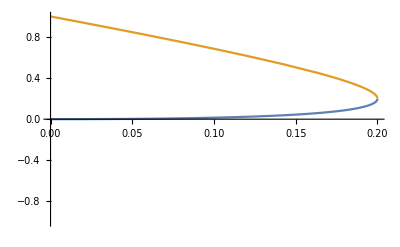

Stability of fixed point 4

Instable eigen1

False

Instable eigen2

1/5<z≤1

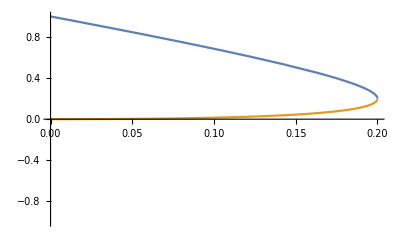

```mathematica
Clear[der2,eigen,der2WithSol];
der2=Simplify[{{D[systemCIzealotsSym[[1]],A], D[systemCIzealotsSym[[1]],B]}, {D[systemCIzealotsSym[[2]],A], D[systemCIzealotsSym[[2]],B]}}];
Do[
Print[Style["Stability of fixed point "<>ToString[solN],Bold,FontSize->15,Blue]];
der2WithSol=der2/.fixedPointsCIzealotsSym[[solN]];
"Eigenvalues";
eigen=Eigenvalues[der2WithSol];
Print[Style["Instable eigen1",Italic]];
Print[Reduce[eigen[[1]]>0&&0≤z<=1,z,Reals]];
Print[Style["Instable eigen2",Italic]];
Print[Reduce[eigen[[2]]>0&&0≤z<=1,z,Reals]];
Print[Plot[{fixedPointsCIzealotsSym⟦solN⟧⟦1,2⟧,fixedPointsCIzealotsSym⟦solN⟧⟦2,2⟧},{z,0,1},PlotRange->{-1,1},GridLines->{{1/3},{}}]];
,{solN,Range[1,Length[fixedPointsCIzealotsSym]]}]
```

#### The stable point(s) pre-bifurcation are n. 3 and n.4:

```mathematica
FullSimplify[fixedPointsCIzealotsSym[[4,1,2]]]
(*Collect[fixedPointsCIzealotsSym[[2,1,2]],q-1]*)
TeXForm[%]
FullSimplify[fixedPointsCIzealotsSym[[4,2,2]]]
(*Collect[fixedPointsCIzealotsSym[[2,1,2]],q-1]*)
TeXForm[%]
```

1/2 (1-3 z+√(1-6 z+5 z^2))

1/2 (1-3 z-√(1-6 z+5 z^2))

\frac{1}{2} \left(-\sqrt{5 z^2-6 z+1}-3 z+1\right)

### Analysis of the system with the Dynamica plugin

#### Cross - inhibition model with zealots

```mathematica
sysCI2EqZealotASym=DynamicalSystem[{
q(A+z)(1-A-B-2z)- A (B+z),
(B+z) (1-A-B-2z)-q B (A+z)},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{q,0.0001,2.15},{z,0,0.5}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{q,z}]

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,B,q}={0.9999,0,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,B,q}={1.,0,0.0001}

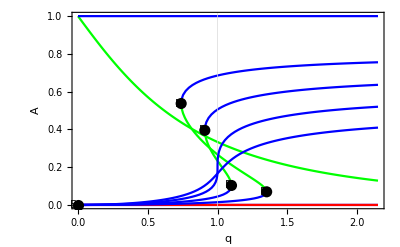

```mathematica
zRange=Join[{0},Range[0.1,0.25,0.05]];
(*zRange=Range[0,0.5,0.1];*)
Show[
Table[
DisplayBifurcationDiagram[sysCI2EqZealotASym/.{z->zz},q,StateVariables->{A},
GridLines->{{1},{}}],{zz,zRange}
]
]
```

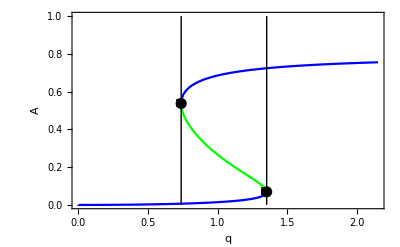

```mathematica
Show[
DisplayBifurcationDiagram[sysCI2EqZealotASym/.{z->0.1},q,StateVariables->{A}],
Graphics[{
Line[{{bifPointCIzealotAsymFuncLowQ/.{z->0.1},0},{bifPointCIzealotAsymFuncLowQ/.{z->0.1},1}}],
Line[{{bifPointCIzealotAsymFuncHighQ/.{z->0.1},0},{bifPointCIzealotAsymFuncHighQ/.{z->0.1},1}}]
}]
]
```

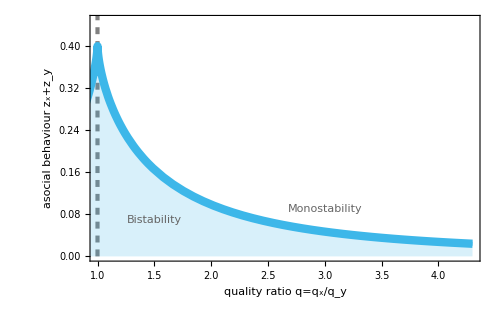

```mathematica
maxQ=4.3;
saveImg=False;
plt=Show[
Plot[2*bifPointCIzealotAsym,{q,0,maxQ},PlotRange->Full,
PlotStyle->Directive[{colours[[2]],Thickness[lineThickness/2]}]
],
Graphics[{
Style[Line[{{1,0},{1,1}}],Directive[{Gray,Dashed,Thickness[lineThickness/2]}]]
}],
Plot[2*bifPointCIzealotAsym,{q,0,maxQ},PlotRange->Full,
PlotStyle->Directive[{colours[[2]],Thickness[lineThickness]}],Filling->0
],
Graphics[{Style[Text["Bistability",{1.5,0.07}],Directive[{textSize,GrayLevel[0.4]}]],Style[Text["Monostability",{3.,0.091}],Directive[{textSize,GrayLevel[0.4]}]]
}],
PlotRange->{{1,maxQ},{0,0.45}},Axes->False,FrameStyle->Directive[{Thickness[.005]}],
PlotRangePadding->0,
ImageSize->500,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"quality ratio q=q_x/q_y","asocial behaviour z_x+z_y"}
]
If[saveImg,Export["/Volumes/GoogleDrive/My Drive/OpenMatter/Eliseo/SymmetryBreakingWithZealots/graphics/fig4_panels/ODE-CI-bifurc-zq.pdf",plt]];
```

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,B,q}={0.9999,0,0.0001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {A,B,q}={1.,0,0.0001}

Found 2 stable branches and 2 saddle branches

Found 2 stable branches and 1 saddle branches

Found 2 stable branches and 1 saddle branches

Found 1 stable branches and 0 saddle branches

Found 1 stable branches and 0 saddle branches

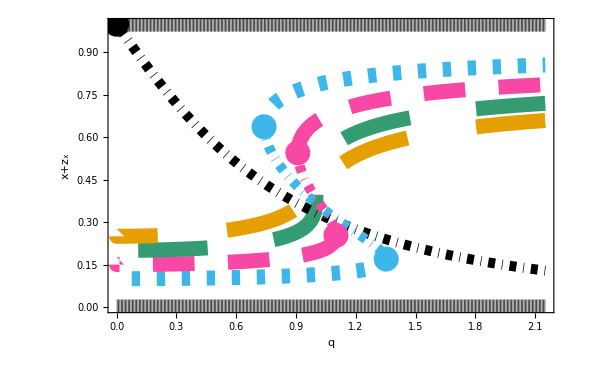

```mathematica
saveImg=False;
zTextSize=32;
labelSize=38;
tickSize=30;

bifPointSize=0.03;
zRange=Join[{0},Range[0.1,0.25,0.05]];
stableBrQratioZs=List[];
saddleBrQratioZs=List[];
dashedSyle={0,{0.01,0.02},{0.05,0.04},{0.1,0.08},{0.15,0.1},{0.0044,0.004}};
(*zText=Range[1.03,1.03-0.081*Length[zRange],-0.06];*)
(*zText={{0.2,1},{0.65,0.6},{0.85,0.55},{1.0,0.525},{1.12,0.5},{1.1,0.45}};*)
(*zText={{1.65,1},{1.65,0.88},{1.7,0.78},{1.7,0.7},{1.65,0.6},{1.1,0.45}};*)
(*zText={{2.22,1},{2.22,0.86},{2.22,0.79},{2.22,0.72},{2.22,0.66},{1.1,0.45}};*)
zText={{2.22,1.04},{2.22,0.93},{2.22,0.82},{2.22,0.71},{2.22,0.6},{1.1,0.45}};
Do[
eb=EquilibriumBranches[sysCI2EqZealotASym/.{z->zRange⟦zi⟧},q];
stableBrQratio=List[];
saddleBrQratio=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBrQratio,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBrQratio,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBrQratio]]<>" stable branches and "<>ToString[Length[saddleBrQratio]]<>" saddle branches"]
AppendTo[stableBrQratioZs,stableBrQratio];
AppendTo[saddleBrQratioZs,saddleBrQratio];
,{zi,Range[1,Length[zRange]]}
]
(*zText=Table[stableBrQratioZs[[zi]][[-1]][[4]][[5,{3,1}]],{zi,Range[1,Length[zRange]]}];*)

plt=Show[
Table[Table[
ListLinePlot[stableBrQratioZs[[zi]][[sb]][[4]][[All,{3,1}]]+ConstantArray[{0,zRange[[zi]]},Length[stableBrQratioZs[[zi]][[sb]][[4]][[All,{3,1}]]]],PlotStyle->Directive[{colours[[zi]],Thickness[lineThickness*1.5],Dashing[dashedSyle[[zi]]]}]
],
{sb,Range[1,Length[stableBrQratioZs[[zi]]]]}],{zi,Range[1,Length[zRange]]} ],
Table[Table[
ListLinePlot[saddleBrQratioZs[[zi]][[sb]][[4]][[All,{3,1}]]+ConstantArray[{0,zRange[[zi]]},Length[saddleBrQratioZs[[zi]][[sb]][[4]][[All,{3,1}]]]],PlotStyle->Directive[{colours[[zi]],Thickness[lineThickness],DotDashed}](*Dashing[{0.001,0.02}]*)
],
{sb,Range[1,Length[saddleBrQratioZs[[zi]]]]}],{zi,Range[1,Length[zRange]]} ],
Table[
Graphics[
Style[Text[If[zi<3||zi==Length[zRange],"z=","z="]<>ToString[zRange[[zi]]],zText[[zi]],{-1,0}],
Directive[{colours[[zi]],zTextSize,Bold}],TextAlignment->Right,Background->None
]
]
(*[saddleBrQratioZs[[zi]][[1]][[4]][[-1,{2,1}]],*)
,
{zi,Range[1,Length[zRange]]} ],
Table[
Graphics[{colours[[zi]],PointSize[bifPointSize],
If[zi==1,
Point[{0,1}]
,
Point[{
{bifPointCIzealotAsymFuncLowQ/.{z->zRange[[zi]]},
Re[(fixedPointsCIzealots/.{z->zRange[[zi]],q->bifPointCIzealotAsymFuncLowQ/.{z->zRange[[zi]]}})[[4,1,2]]]+zRange[[zi]]},
{bifPointCIzealotAsymFuncHighQ/.{z->zRange[[zi]]},
Re[(fixedPointsCIzealots/.{z->zRange[[zi]],q->bifPointCIzealotAsymFuncHighQ/.{z->zRange[[zi]]}})[[4,1,2]]]+zRange[[zi]]}}]
]
}]
,
{zi,Range[1,Length[zRange]-2]} ],
ImagePadding->{{95,101},{95,10}},PlotRangeClipping->False,
PlotRange->{{0,2.15},{0,1}},Axes->False,FrameStyle->Directive[{Thickness[.005]}],
ImageSize->600,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
(*FrameLabel->{"quality ratio q=q_x/q_y","population x+z_x"}*)
FrameLabel->{"q","x+z_x"}
]
If[saveImg,Export[projectHomeDir<>"/graphics/fig4_panels/ODE-CI-majority.pdf",plt]];
```

#### Direct switch model with zealots

```mathematica
sysDS2EqZealotASym=DynamicalSystem[{
(q-1)A (1-A-2z)+z(q(1-A-2z)-A )},
{{A,-0.01,1+0.01}},
{{q,0.0001,2.15},{z,0,0.5}}]
```

DynamicalSystem[«1 ODE»,{A},{q,z}]

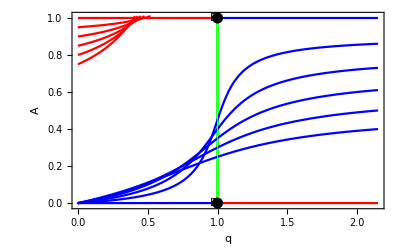

```mathematica
Show[
Table[
DisplayBifurcationDiagram[sysDS2EqZealotASym/.{z->zz},q,GridLines->{{1},{}}],{zz,Range[0,0.25,0.05]}
]
]
```

Found 2 stable branches and 4 saddle branches

Found 1 stable branches and 0 saddle branches

Found 1 stable branches and 0 saddle branches

Found 1 stable branches and 0 saddle branches

«1 more identical outputs»

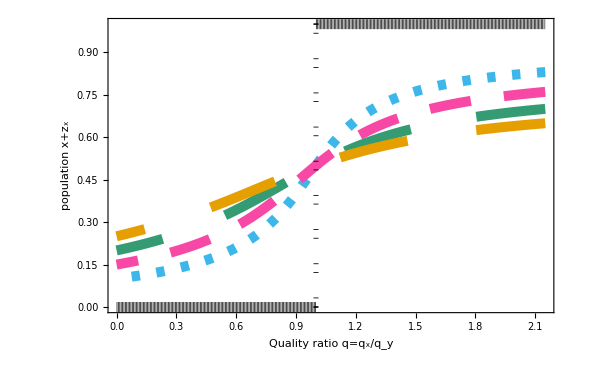

```mathematica
zRange=Join[{0},Range[0.1,0.25,0.05]];
stableBrQratioZs=List[];
saddleBrQratioZs=List[];
dashedSyle={0,{0.01,0.02},{0.05,0.04},{0.1,0.08},{0.15,0.1},0.0044};
zText=Join[{1},Range[0.9,0.83-0.081*Length[zRange],-0.1]];(*Table[{2.1,1-zRange[[zi]]},{zi,Range[1,Length[zRange]]}];*)
Do[
eb=EquilibriumBranches[sysDS2EqZealotASym/.{z->zRange⟦zi⟧},q];
stableBrQratio=List[];
saddleBrQratio=List[];
Do[
If[branch[[2]]==Symbol["Stable"],
AppendTo[stableBrQratio,branch]];
If[branch[[2]]==Symbol["Saddle"],
AppendTo[saddleBrQratio,branch]];
,{branch,eb[[1]]}];
Print["Found "<>ToString[Length[stableBrQratio]]<>" stable branches and "<>ToString[Length[saddleBrQratio]]<>" saddle branches"]
AppendTo[stableBrQratioZs,stableBrQratio];
AppendTo[saddleBrQratioZs,saddleBrQratio];
,{zi,Range[1,Length[zRange]]}
]

plt=Show[
Table[Table[
ListLinePlot[stableBrQratioZs[[zi]][[sb]][[4]][[All,{2,1}]]+ConstantArray[{0,zRange[[zi]]},Length[stableBrQratioZs[[zi]][[sb]][[4]][[All,{2,1}]]]],PlotStyle->Directive[{colours[[zi]],Thickness[lineThickness],Dashing[dashedSyle[[zi]]]}]
],
{sb,Range[1,Length[stableBrQratioZs[[zi]]]]}],{zi,Range[1,Length[zRange]]} ],
Table[Table[
ListLinePlot[saddleBrQratioZs[[zi]][[sb]][[4]][[All,{2,1}]]+ConstantArray[{0,zRange[[zi]]},Length[saddleBrQratioZs[[zi]][[sb]][[4]][[All,{2,1}]]]],PlotStyle->Directive[{colours[[zi]],Thickness[lineThickness/2],Dashing[{0.001,0.04}]}]
],
{sb,Range[1,Length[saddleBrQratioZs[[zi]]]]}],{zi,Range[1,Length[zRange]]} ],
Table[
Graphics[
Style[Text["z="<>ToString[zRange[[zi]]],{2.22,zText[[zi]]},{-1,0}],
Directive[{colours[[zi]],zTextSize,Bold}],TextAlignment->Right
]
]
(*[saddleBrQratioZs[[zi]][[1]][[4]][[-1,{2,1}]],*)
,
{zi,Range[1,Length[zRange]]} ],
(*Table[
ListLinePlot[stableBrQratioZs[[zi]][[sb]][[4]][[All,{2,1}]]],{sb,Range[1,Length[stableBrQratioZs[[zi]]]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}],
*)(*ListLinePlot[Join[Transpose[{saddleBrQratio[[1]][[4]][[All,3]]}],Transpose[{saddleBrQratio[[1]][[4]][[All,1]]-saddleBrQratio[[1]][[4]][[All,2]]}],2],PlotStyle->{colours[[3]],Thickness[lineThickness],Dashing[{0.03,0.03}]}],
ListLinePlot[Table[Join[Transpose[{stableBrQratio[[sb]][[4]][[All,3]]}],Transpose[{stableBrQratio[[sb]][[4]][[All,2]]-stableBrQratio[[sb]][[4]][[All,1]]}],2],{sb,Range[1,Length[stableBrQratio]]}],PlotStyle->Directive[{colours[[1]],Thickness[lineThickness]}]],
*)(*Style[Text["CROSS-INHIBITION",{0.5,1.1}],Directive[{textSize,Gray},Background->White]]}],
*)ImagePadding->{{100,105},{100,15}},PlotRangeClipping->False,
PlotRange->{{0,2.15},{0,1}},Axes->False,FrameStyle->Directive[{Thickness[.005]}],
ImageSize->600,Frame->True,LabelStyle->labelSize,FrameTicksStyle->tickSize,
FrameLabel->{"Quality ratio q=q_x/q_y","population x+z_x"}
]
Export["/Volumes/GoogleDrive/My Drive/OpenMatter/Eliseo/SymmetryBreakingWithZealots/tmp_imgs/ODE-VM-majority.pdf",plt];
```